```mathematica
u[x_,y_] = Simplify[Re[ComplexExpand[(x+I y)Tanh[π/2 Sinh[(x+I y)]]]], Assumptions->{Element[{x,y},Reals]}];
v[x_,y_] = Simplify[Im[ComplexExpand[(x+I y)Tanh[π/2 Sinh[(x+I y)]]]], Assumptions->{Element[{x,y},Reals]}];
```

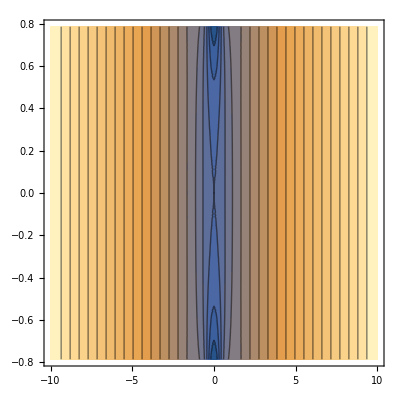

```mathematica
ContourPlot[{u[x,y]},{x,-10,10},{y,-π/4,π/4},Contours->20]
```

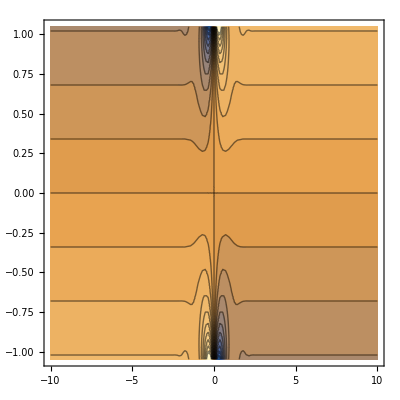

```mathematica
ContourPlot[{v[x,y]},{x,-10,10},{y,-π/3,π/3},Contours->20]
```

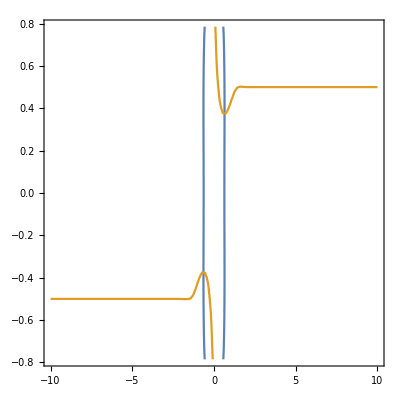

```mathematica
ContourPlot[{u[x,y] == 0.5,v[x,y] == 0.5},{x,-10,10},{y,-π/4,π/4}]
```

```mathematica
Solve[Normal@Series[1/2 π z Cosh[z] Sech[1/2 π Sinh[z]]^2+Tanh[1/2 π Sinh[z]],{z,0,3}] == 0,z]
```

{{z→0},{z→-√(6/(-2+π^2))},{z→√(6/(-2+π^2))}}

```mathematica
z Tanh[π/2 Sinh[z]]/.z-> I y
```

-y Tan[1/2 π Sin[y]]